```mathematica
b=Classify[{{0.697,0.460}->"A",{0.774,0.376}->"A",{0.634,0.264}->"A",{0.608,0.318}->"A",{0.556,0.215}->"A",{0.403,0.237}->"A",{0.481,0.149}->"A",{0.437,0.211}->"A",{0.666,0.091}->"B",{0.243,0.267}->"B",{0.245,0.057}->"B",{0.343,0.099}->"B",{0.593,0.042}->"B",{0.719,0.103}->"B",{0.360,0.370}->"B",{0.593,0.042}->"B",{0.719,0.103}->"B"
}]
```

5.555

16.321

-6.04

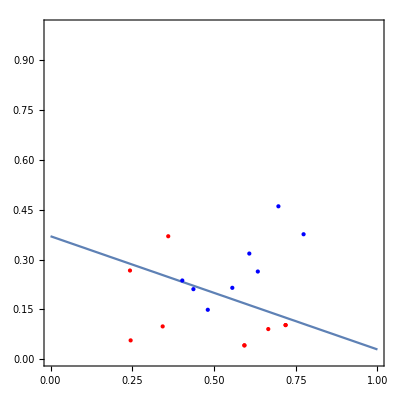

```mathematica
a=5.555
b=16.321
c=-6.04
p1=ContourPlot[(1/(1+Exp[-a*x-b*y-c]))==0.5,{x,0,1},{y,0,1}]
p2=ListPlot[{{0.697,0.460},{0.774,0.376},{0.634,0.264},{0.608,0.318},{0.556,0.215},{0.403,0.237},{0.481,0.149},{0.437,0.211}},PlotStyle->{Blue,PointSize[Large]}]
p3=ListPlot[{{0.666,0.091},{0.243,0.267},{0.245,0.057},{0.343,0.099},{0.593,0.042},{0.719,0.103},{0.360,0.370},{0.593,0.042},{0.719,0.103}},
PlotStyle->{Red,PointSize[Large]}]

Show[p1,p2,p3]
```